```mathematica
Clear[f,g,h,k,ff,kk,ll,gg]
allColors=ColorData["Legacy"][[3,1]];
firstCols=Join[{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"},{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"}];
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
```

```mathematica
(*von Koch Cartoon*)
```

```mathematica
f[x_]:=0/;0<=x<=1/3
f[x_]:=6*x-2/;1/3<x<=1/2
f[x_]:=-6*x+4/;1/2<x<=2/3
f[x_]:=0/;2/3<x<=1
```

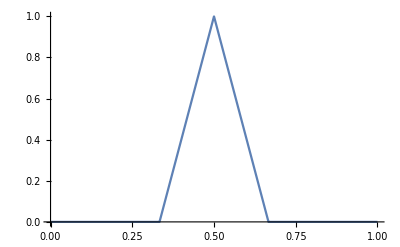

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

f[Mod[Abs[x],1]]

```mathematica
Plot[ff[x],{x,0,1}]
```

-Graphics-

```mathematica
g[x_,y_]:=Min[f[x]*f[y],f[x]+f[y]]
```

```mathematica
a=Flatten[ParallelTable[{x,y,g[x,y]},{x,0,1,1/225},{y,0,1,1/225}],1];
```

```mathematica
ga=ListPointPlot3D[a,PlotRange->All,ImageSize->2000,ColorFunction->Hue,PlotStyle->PointSize[0.001]];
```

```mathematica
gb=ParametricPlot3D[{x,y,g[x,y]},{x,0,1},{y,0,1},PlotRange->All,ImageSize->Full,ColorFunction->Hue,Mesh->None,PlotPoints->100];
```

```mathematica
gout=Show[{ga,gb},ViewPoint->{2,2,2}];
```

```mathematica
gout2=Show[gout,ViewPoint->Above];
```

```mathematica
g3=Show[gout,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[gout,ViewPoint->Right];
```

```mathematica
Export["Von_Koch_Minimum_Field3d_grid.jpg" ,GraphicsGrid[{{gout,gout2},{g3,g4}},ImageSize->{{4000,4000}}]]
```

Von_Koch_Minimum_Field3d_grid.jpg

```mathematica
gg[x_,y_]=g[Mod[Abs[x],1],Mod[Abs[x],1]]
```

Min[2 f[Mod[Abs[x],1]],f[Mod[Abs[x],1]]^2]

```mathematica
(*b=Flatten[ParallelTable[{x,y,gg[x,y]},{x,0,1,1/100},{y,0,1,1/100}],1];
gc=ListPointPlot3D[b,PlotRange->All,ImageSize->Full,ColorFunction->Hue,PlotStyle->PointSize[0.001]]
gd=ParametricPlot3D[{x,y,gg[x,y]},{x,0,1},{y,0,1},PlotRange->All,ImageSize->Full,ColorFunction->Hue,Mesh->None,PlotPoints->100];
gout=Show[{gc,gd}]*)
```

```mathematica
s0=N[Log[2]/Log[3]];
kk[x_,y_]=Sum[gg[3^k*x,3^k*y]/3^(s0*k),{k,0,20}];
ll[x_,y_]=Sum[gg[3^k*(x+1/2),3^k*(y+1/2)]/3^(s0*k),{k,0,20}];
jj[x_,y_]=Sum[gg[3^k*(x-1/2),3^k*(y-1/2)]/3^(s0*k),{k,0,20}];
```

```mathematica
nn=1000
```

1000

```mathematica
p[n_,m_]={kk[n/nn,m/nn],ll[m/nn,m/nn],jj[n/nn,m/nn]};
```

```mathematica
aa=Flatten[ParallelTable[p[n,m],{n,0,nn},{m,0,nn}],1];
```

```mathematica
Length[aa]
```

1002001

```mathematica
g0=ListPointPlot3D[aa,AspectRatio->Automatic,ColorFunction->"CMYKColors",ImageSize->1000,PlotRange->All];
```

```mathematica
Export["Biscuit_vonKoch_minimum_Field3d1000_g0.jpg",g0]
```

Biscuit_vonKoch_minimum_Field3d1000_g0.jpg

```mathematica
dlst=ParallelTable[1+Mod[Floor[1+(1+Floor[24*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]

ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

2

70

```mathematica
g2=Graphics3D[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->1500,Axes->False,Background->Black,PlotRange->All,ViewPoint->{2,2,2}];
```

```mathematica
Export["Biscuit_Von_Koch_minimum_Field3d1000_g2.jpg",g2]
```

Biscuit_Von_Koch_minimum_Field3d1000_g2.jpg

```mathematica
g3=Show[g2,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g2,ViewPoint->Right];
```

```mathematica
g5=Show[g2,ViewPoint->Above];
```

```mathematica
Export["biscuit_Von_Koch_Minimum_Field3d1000_grid.jpg" ,GraphicsGrid[{{g2,g5},{g3,g4}},ImageSize->{{4000,4000}}]]
```

biscuit_Von_Koch_Minimum_Field3d1000_grid.jpg

```mathematica
g2=ListSurfacePlot3D[aa,ColorFunction->"Rainbow",ImageSize->2000,MaxPlotPoints->100,ViewPoint->{2,2,2}];
```

```mathematica
g3=Show[g2,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g2,ViewPoint->Right];
```

```mathematica
g5=Show[g2,ViewPoint->Above];
```

```mathematica
Export["biscuit_Von_Koch_Minimum_Field3d1000_ListSurfacePlot3D_grid2.jpg" ,GraphicsGrid[{{g2,g5},{g3,g4}},ImageSize->{{4000,4000}}]]
```

biscuit_Von_Koch_Minimum_Field3d1000_ListSurfacePlot3D_grid2.jpg

```mathematica
(*end*)
```